Isolate the rural and urban data into ordered pairs

```mathematica
ruralData := {{1960,9524815},{1961,9788594},{1962,10061090},{1963,10342570},{1964,10633184},{1965,10933256},{1966,11242464},{1967,11561238},{1968,11859675},{1969,12161341},{1970,12472681},{1971,12793744},{1972,13122864},{1973,13456155},{1974,13788022},{1975,14114660},{1976,14433667},{1977,14745918},{1978,15051616},{1979,15434202},{1980,15840019},{1981,16257170},{1982,16684151},{1983,17119735},{1984,17560697},{1985,18006460},{1986,18452180},{1987,18899561},{1988,19357749},{1989,19879704},{1990,20444353},{1991,21051652},{1992,21694063},{1993,22346853},{1994,22975670},{1995,23558308},{1996,24085271},{1997,24568427},{1998,25031766},{1999,25509469},{2000,26025846},{2001,26589202},{2002,27192241},{2003,27758065},{2004,28325265},{2005,28897340},{2006,29472457},{2007,30055023},{2008,30647132},{2009,31254802},{2010,31878948},{2011,32520460},{2012,33175682},{2013,33843165},{2014,34520751},{2015,35205372},{2016,35896823},{2017,36593461},{2018,37293015},{2019,37993577},{2020,38691642}}

urbanData := {{1960,527336},{1961,558101},{1962,590864},{1963,625626},{1964,662491},{1965,701581},{1966,742978},{1967,786950},{1968,865844},{1969,959246},{1970,1062806},{1971,1177954},{1972,1305476},{1973,1446116},{1974,1600911},{1975,1770568},{1976,1956494},{1977,2159304},{1978,2381140},{1979,2542017},{1980,2698244},{1981,2863513},{1982,3039166},{1983,3224815},{1984,3421078},{1985,3627339},{1986,3844102},{1987,4071647},{1988,4313058},{1989,4532040},{1990,4759495},{1991,5004953},{1992,5267141},{1993,5540351},{1994,5816979},{1995,6090820},{1996,6359252},{1997,6624426},{1998,6892435},{1999,7172771},{2000,7473331},{2001,7796647},{2002,8142549},{2003,8579713},{2004,9054501},{2005,9552983},{2006,10076209},{2007,10626393},{2008,11206812},{2009,11819028},{2010,12467584},{2011,13153060},{2012,13877351},{2013,14639967},{2014,15439812},{2015,16277266},{2016,17152408},{2017,18066884},{2018,19020429},{2019,20011884},{2020,21042571}}

dataLength := Length[urbanData]
totalData := Table[{ruralData[[i, 1]], ruralData[[i, 2]] + urbanData[[i, 2]]}, {i, 1, dataLength}]
```

Put both the datasets into matrix form

```mathematica
MatrixForm[ruralData]
MatrixForm[urbanData]
```

(1960 | 9524815
1961 | 9788594
1962 | 10061090
1963 | 10342570
1964 | 10633184
1965 | 10933256
1966 | 11242464
1967 | 11561238
1968 | 11859675
1969 | 12161341
1970 | 12472681
1971 | 12793744
1972 | 13122864
1973 | 13456155
1974 | 13788022
1975 | 14114660
1976 | 14433667
1977 | 14745918
1978 | 15051616
1979 | 15434202
1980 | 15840019
1981 | 16257170
1982 | 16684151
1983 | 17119735
1984 | 17560697
1985 | 18006460
1986 | 18452180
1987 | 18899561
1988 | 19357749
1989 | 19879704
1990 | 20444353
1991 | 21051652
1992 | 21694063
1993 | 22346853
1994 | 22975670
1995 | 23558308
1996 | 24085271
1997 | 24568427
1998 | 25031766
1999 | 25509469
2000 | 26025846
2001 | 26589202
2002 | 27192241
2003 | 27758065
2004 | 28325265
2005 | 28897340
2006 | 29472457
2007 | 30055023
2008 | 30647132
2009 | 31254802
2010 | 31878948
2011 | 32520460
2012 | 33175682
2013 | 33843165
2014 | 34520751
2015 | 35205372
2016 | 35896823
2017 | 36593461
2018 | 37293015
2019 | 37993577
2020 | 38691642)

(1960 | 527336
1961 | 558101
1962 | 590864
1963 | 625626
1964 | 662491
1965 | 701581
1966 | 742978
1967 | 786950
1968 | 865844
1969 | 959246
1970 | 1062806
1971 | 1177954
1972 | 1305476
1973 | 1446116
1974 | 1600911
1975 | 1770568
1976 | 1956494
1977 | 2159304
1978 | 2381140
1979 | 2542017
1980 | 2698244
1981 | 2863513
1982 | 3039166
1983 | 3224815
1984 | 3421078
1985 | 3627339
1986 | 3844102
1987 | 4071647
1988 | 4313058
1989 | 4532040
1990 | 4759495
1991 | 5004953
1992 | 5267141
1993 | 5540351
1994 | 5816979
1995 | 6090820
1996 | 6359252
1997 | 6624426
1998 | 6892435
1999 | 7172771
2000 | 7473331
2001 | 7796647
2002 | 8142549
2003 | 8579713
2004 | 9054501
2005 | 9552983
2006 | 10076209
2007 | 10626393
2008 | 11206812
2009 | 11819028
2010 | 12467584
2011 | 13153060
2012 | 13877351
2013 | 14639967
2014 | 15439812
2015 | 16277266
2016 | 17152408
2017 | 18066884
2018 | 19020429
2019 | 20011884
2020 | 21042571)

Normalize both of the datasets to have x be in years after 1960

```mathematica
ruralNormedData := Table[{ruralData[[i, 1]] - 1960, ruralData[[i, 2]]}, {i, 1, dataLength}]
urbanNormedData := Table[{urbanData[[i, 1]] - 1960, urbanData[[i, 2]]}, {i, 1, dataLength}]
```

Plot the urban and rural data

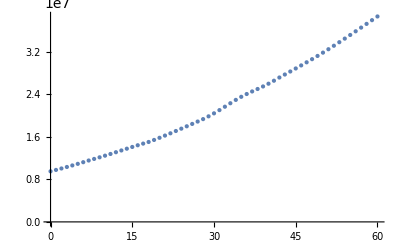

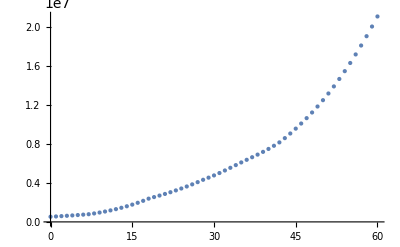

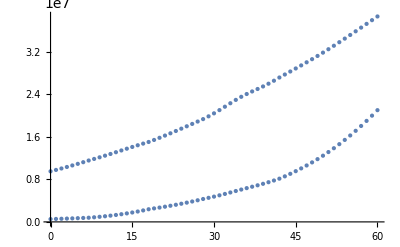

```mathematica
ruralGraph = ListPlot[ruralNormedData, PlotStyle->AbsolutePointSize[Small]]
urbanGraph = ListPlot[urbanNormedData, PlotStyle->AbsolutePointSize[Small]]
Show[ruralGraph, urbanGraph]
```

The rural data almost approximates a linear relationship

We begin by modeling the rural population by fitting a line to the data

7.15227×10^6+488736. x

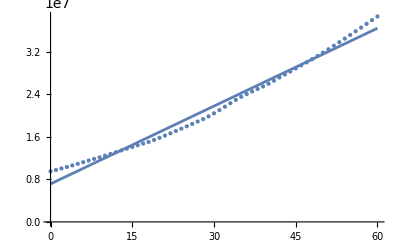

```mathematica
ruralFit = Fit[ruralNormedData, {x, 1}, x]
ruralLinePlot := Plot[ruralFit, {x, 0, 60}]
Show[ruralGraph, ruralLinePlot]
```

Plot the residual to see if this is anything

ListPlot::lpn: (7.15227×10^6+488736. x)[FitResiduals] is not a list of numbers or pairs of numbers.

ListPlot[(7.15227×10^6+488736. x)[FitResiduals]]

We now model the urban population by plotting the change in the graph.

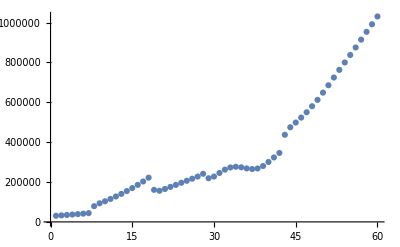

General::ivar: 0.00122571 is not a valid variable.

General::ivar: 1.22572 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{{1,30765},{2,32763},{3,34762},{4,36865},{5,39090},{6,41397},{7,43972},{8,78894},{9,93402},{10,103560},«50»},].

Show[{{1,30765},{2,32763},{3,34762},{4,36865},{5,39090},{6,41397},{7,43972},{8,78894},{9,93402},{10,103560},{11,115148},{12,127522},{13,140640},{14,154795},{15,169657},{16,185926},{17,202810},{18,221836},{19,160877},{20,156227},{21,165269},{22,175653},{23,185649},{24,196263},{25,206261},{26,216763},{27,227545},{28,241411},{29,218982},{30,227455},{31,245458},{32,262188},{33,273210},{34,276628},{35,273841},{36,268432},{37,265174},{38,268009},{39,280336},{40,300560},{41,323316},{42,345902},{43,437164},{44,474788},{45,498482},{46,523226},{47,550184},{48,580419},{49,612216},{50,648556},{51,685476},{52,724291},{53,762616},{54,799845},{55,837454},{56,875142},{57,914476},{58,953545},{59,991455},{60,1030687}},-Graphics-]

```mathematica
urbanChange := Table[{urbanNormedData[[i + 1, 1]], urbanNormedData[[i + 1, 2]] - urbanNormedData[[i, 2]]}, {i, 1, dataLength - 1}]
urbanChangePlot = ListPlot[urbanChange]
urbanChangeLine := Fit[urbanChange, {x, 1}, x]
Show[urbanChange, Plot[urbanChangeLine,{x, 0, 60}]]
```

The change in the population doesn’t seem to have a linear relationship with the years after 1960, so we must try something else. 

If the relationship is exponential, then the logarithm of the x and y axis will be linear

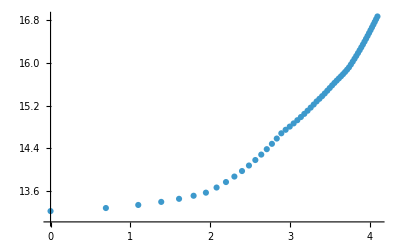

```mathematica
urbanLog := Table[{Log[urbanNormedData[[i, 1]]], Log[urbanNormedData[[i, 2]]]}, {i, 1, dataLength}]
urbanLogPlot = ListPlot[urbanLog]
```